```mathematica
AB=l1=93.75;
BC=l2=421.875;
h=187.5;
α=0.22409309230137084;
CD=l3=195.;
ls2=0.3BC;
ls3=0.3BC;
pmax=8 10^5;
pmin=-8 10^-4;
m2=12;
m3=7.8;
Js2=0.214;
Js1=0.025;
```

```mathematica
f[x_]:=Piecewise[{{ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))],Sin[x]≥ 0},{2Pi-ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))],Sin[x]< 0}}]
```

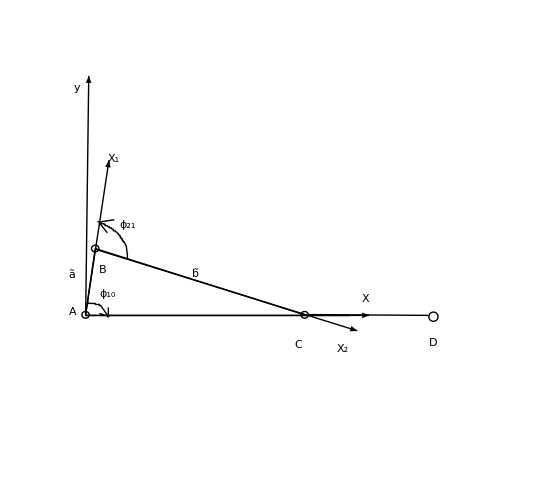

```mathematica
Clear[f]
```

```mathematica
a:={AB,0,0};
b:={BC,0,0};
s2:={ls2,0,0};
s3:={ls3,0,0};
```

```mathematica
M10[x_]:={{Cos[x],-Sin[x],0},{Sin[x],Cos[x],0},{0,0,1}}
M21[x_]:={{Cos[f[x]],Sin[f[x]],0},{-Sin[f[x]],Cos[f[x]],0},{0,0,1}}
M20[x_]:=M21[x].M10[x]
```

```mathematica
Rb[x_]:=M10[x].a
Rc[x_]:=M10[x].a+M20[x].b
Rd[x_]:=Rc[x]+{CD,0,0}
Rs2[x_]:=M10[x].a+M20[x].s2
Rs3[x_]:=Rc[x]+{ls3,0,0}
```

```mathematica
Animate[
pA:={0,0};
pB:=Rb[ϕ][[1;;2]];
pC:=Rc[ϕ][[1;;2]];
pD:=Rd[ϕ][[1;;2]];
pS3:=Rs3[ϕ][[1;;2]];
pS2:=Rs2[ϕ][[1;;2]];
Graphics[{Line[{pA,pB}],Line[{pB,pC}],Line[{pC,pD}],Point[pS2],Point[pS3],

Circle[#,5]&/@{pA,pB,pC},
FontSize->14,Text[#[[1]],#[[2]] +{15,15}]&/@{ {"A",pA}, {"B",pB}, {"C",pC},{"S3",pS3},{"S2",pS2},{"D",pD}}


},
Axes->False,PlotRange->{{-AB-5,AB+BC+CD+50},{-AB-50,AB+50}}],{ϕ,0,4Pi}]
```

```mathematica
Vb[x_]:=(D[Rb[y],y]/.y->x)[[1;;2]]
Vc[x_]:=(D[Rc[y],y]/.y->x)[[1;;2]]
Vd[x_]:=(D[Rd[y],y]/.y->x)[[1;;2]]
Vs3[x_]:=(D[Rs3[y],y]/.y->x)[[1;;2]]
Vs2[x_]:=(D[Rs2[y],y]/.y->x)[[1;;2]]
```

```mathematica
ab[x_]:=(D[Rb[y],{y,2}]/.y->x)[[1;;2]]
ac[x_]:=(D[Rc[y],{y,2}]/.y->x)[[1;;2]]
ad[x_]:=(D[Rd[y],{y,2}]/.y->x)[[1;;2]]
as3[x_]:=(D[Rs3[y],{y,2}]/.y->x)[[1;;2]]
as2[x_]:=(D[Rs2[y],{y,2}]/.y->x)[[1;;2]]
```

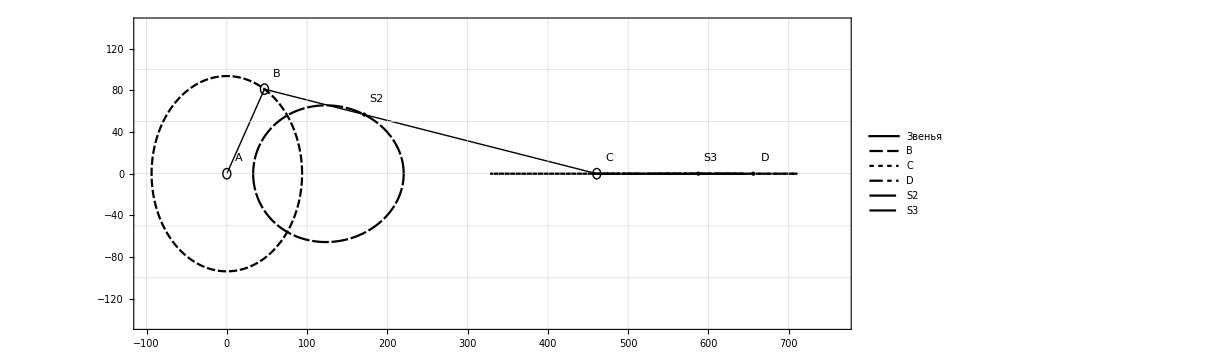

```mathematica
Module[{pA,pB,pC,pD,pS3,pS2,ϕ},
pA:={0,0};
pB:=Rb[ϕ][[1;;2]];
pC:=Rc[ϕ][[1;;2]];
pD:=Rd[ϕ][[1;;2]];
pS3:=Rs3[ϕ][[1;;2]];
pS2:=Rs2[ϕ][[1;;2]];
ϕ=Pi/3;
Show[{Graphics[{PointSize[Large],Thick,Line[{pA,pB}],Line[{pB,pC}],Line[{pC,pD}],Point[pD],Point[pS2],Point[pS3],

Circle[#,5]&/@{pA,pB,pC},
FontSize->14,Text[#[[1]],#[[2]] +{15,15}]&/@{ {"A",pA}, {"B",pB}, {"C",pC},{"S3",pS3},{"S2",pS2},{"D",pD}}


}],
ParametricPlot[{{0,0},Rb[x][[1;;2]],Rc[x][[1;;2]],Rd[x][[1;;2]],Rs2[x][[1;;2]],Rs3[x][[1;;2]]},{x,0,2Pi},PlotTheme->"Monochrome",PlotLegends->{"Звенья","B","C","D","S2","S3"}]
},
Axes->False,Frame->True,GridLines->{Table[100n,{n,-1,10}],Table[50n,{n,-5,5}]},ImageSize->900,PlotRange->{{-AB-5,AB+BC+CD+50},{-AB-50,AB+50}}]]
```

```mathematica
Manipulate[Graphics[{Text["V_B",Vb[x]+0.1Vb[x]],Text["V_C",Vc[x]+{8,8}],Text["V_S2",Vs2[x]+0.1Vs2[x]] , Arrow[{{0,0},#}]&/@{Vb[x],Vc[x],Vs3[x],Vs2[x]}},Axes->True,PlotRange->{{-100,100},{-100,100}}],{x,0.001,2Pi-0.001}]
```

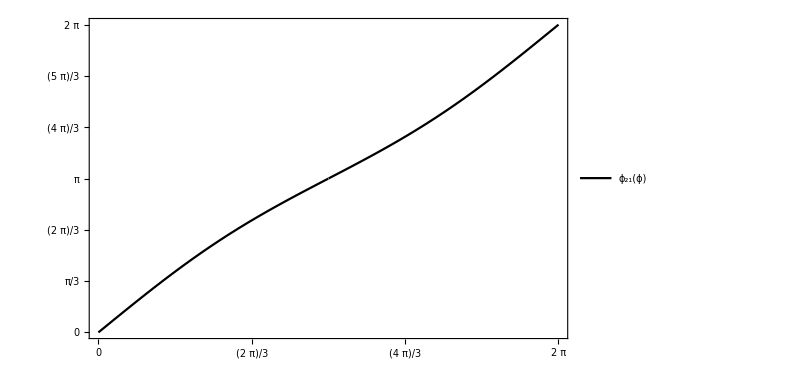

```mathematica
op={Table[Pi /3i,{i,0,8}],Table[Pi /3i,{i,0,8}]};
Plot[f[x],{x,0,2Pi},Frame->True,GridLines->op,FrameTicks->op,PlotTheme->"Monochrome",ImageSize->600,PlotLegends->{"ϕ_21(ϕ)"}]
```

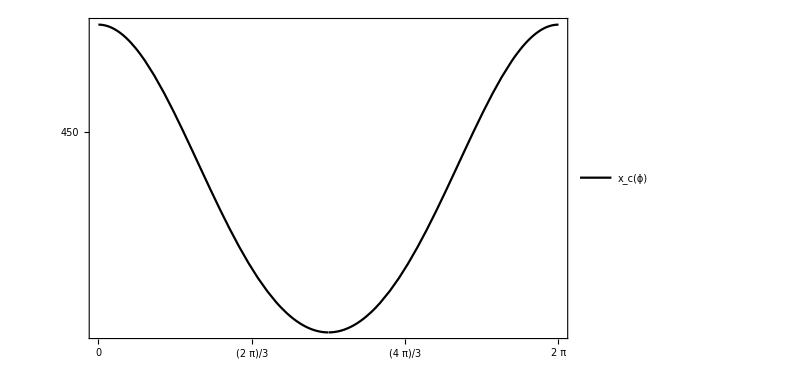

```mathematica
Plot[Rc[x][[1]],{x,0,2Pi},Frame->True,ImageSize->600,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,0,20}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[50i,{i,0,12}]},PlotTheme->"Monochrome",PlotLegends->{"x_c(ϕ)"}]
```

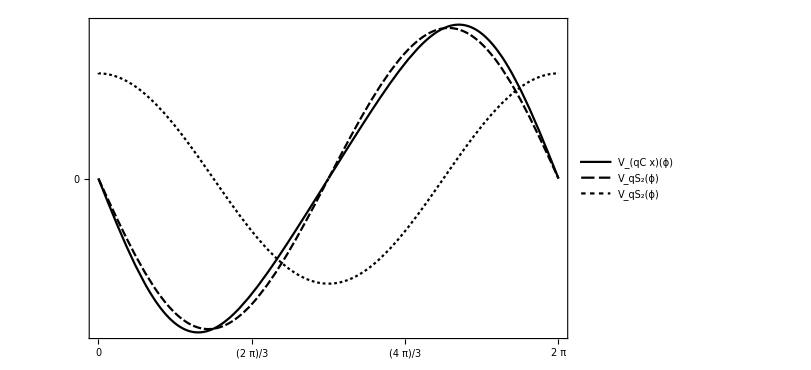

```mathematica
Plot[{Vc[x][[1]],Vs2[x][[1]],Vs2[x][[2]]},{x,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,-8,8}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},ImageSize->600,PlotTheme->"Monochrome",PlotLegends->{"V_(qC x)(ϕ)","V_qS_2(ϕ)","V_qS_2(ϕ)"}]
```

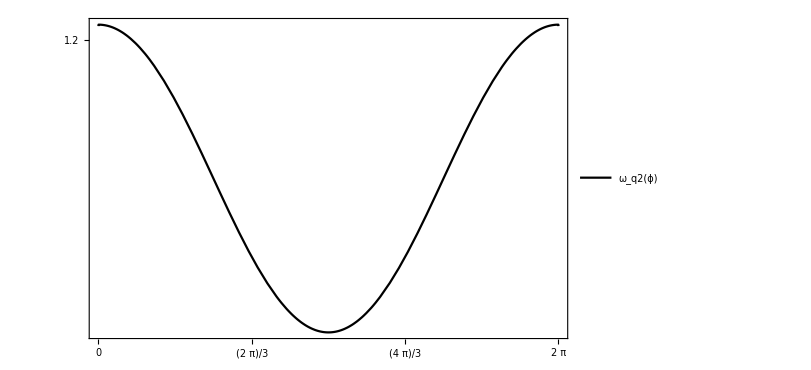

```mathematica
Plot[D[f[x],x]/.x->y,{y,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,0,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.1i,{i,-10,12}]},ImageSize->600,PlotTheme->"Monochrome",PlotLegends->{"ω_q2(ϕ)"}]
```

```mathematica
Manipulate[Graphics[{Text["a_B",ab[x]+0.1ab[x]],Text["a_C",ac[x]+5],Text["a_D",ad[x]+5],Text["a_S2",as2[x]+0.1as2[x]] , Arrow[{{0,0},#}]&/@{ab[x],ac[x],ad[x],as3[x],as2[x]}},Axes->True,PlotRange->{{-100,100},{-100,100}}],{x,0.0001,2Pi-0.0001}]
```

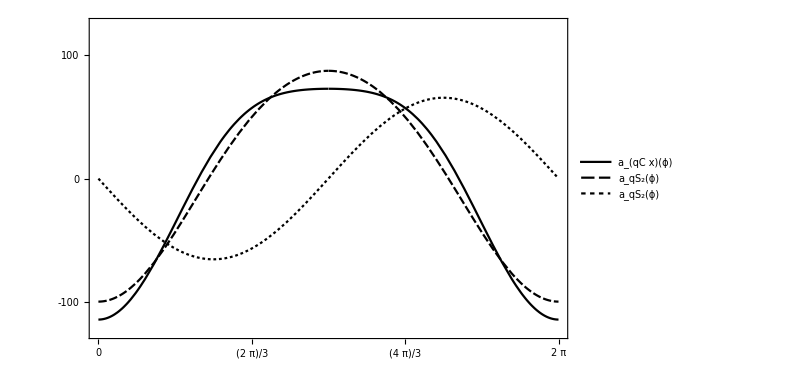

```mathematica
Plot[{ac[x][[1]],as2[x][[1]],as2[x][[2]]},{x,0.001,2Pi-0.001},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[50i,{i,-8,8}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[25i,{i,-10,12}]},PlotRange->125,ImageSize->600,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"a_(qC x)(ϕ)","a_qS_2(ϕ)","a_qS_2(ϕ)"}]
```

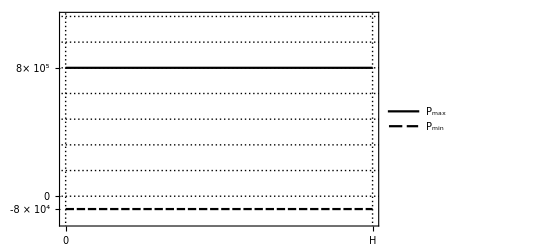

```mathematica
Plot[{10,-1},{x,0,h},Frame->True,GridLines->{{0,h},Table[2i,{i,0,10}]},ExclusionsStyle->Red,FrameTicks->{{0,{h,"H"}},{{-1,"-8 × 10^4"},0,{10,"8× 10^5"}}},PlotRange->{-2,14},PlotTheme->"Monochrome",PlotLegends->{"P_max","P_min"}]
```

```mathematica
Jpr2[x_]:=Js2 (D[f[y],y]/.y->x)^2+m2 Norm[Vs2[x]/1000]^2
```

```mathematica
Jpr3[x_]:=m3 Norm[Vs3[x]/1000]^2
```

```mathematica
JprII[x_]:=Jpr2[x]+Jpr3[x]
```

```mathematica
Plot[{Jpr2[x],Jpr3[x],JprII[x]},{x,0,2Pi}]
```

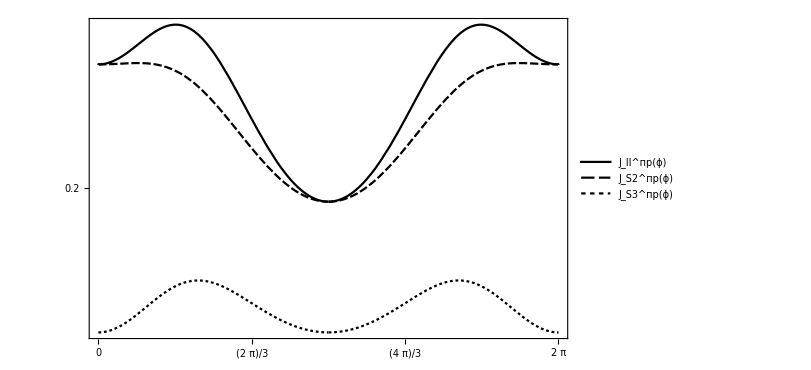

```mathematica
Plot[{JprII[x],Jpr2[x],Jpr3[x]},{x,0,2Pi},Frame->True,FrameTicks->{Table[Pi /3i,{i,0,8}],Table[0.05i,{i,-8,100}]},GridLines->{Table[Pi /3i,{i,0,8}],Table[0.05i,{i,-10,12}]},ImageSize->600,PlotTheme->"Monochrome",ClippingStyle->Red,PlotLegends->{"J_II^(:043f:0440)(ϕ)","J_S2^(:043f:0440)(ϕ)","J_S3^(:043f:0440)(ϕ)"}]
```